## 6

```mathematica
images=Table[ExampleData[{"TestImage", "House"}], {i, 10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
EdgeDetect/@images
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## 5

```mathematica
randomColors=Table[RandomColor[], {i, 10}]
darkerRandomColors = Darker/@randomColors
Table[ColorNegate[c], {c, darkerRandomColors}]
```

{RGBColor[0.548986509263784, 0.9139482476539431, 0.044699123138624675],RGBColor[0.8781063182736175, 0.4262945760858792, 0.15754077076720763],RGBColor[0.6270386061251865, 0.8360143020800999, 0.8089011376870692],RGBColor[0.6791935707324999, 0.5649507779860299, 0.34824718209834526],RGBColor[0.4152035191985306, 0.6950312477122613, 0.9293562345774384],RGBColor[0.11885075562247716, 0.38726186946255203, 0.45864971568536994],RGBColor[0.17237423537002283, 0.11071828030374231, 0.07081746049835491],RGBColor[0.6390069762133761, 0.7099061055427585, 0.8708826410526951],RGBColor[0.00015252723348657682, 0.9911760640271283, 0.3018185808817446],RGBColor[0.25222086857103587, 0.9271070327809405, 0.561861903748641]}

{RGBColor[0.365991006175856, 0.6092988317692954, 0.029799415425749785],RGBColor[0.5854042121824117, 0.2841963840572528, 0.10502718051147175],RGBColor[0.418025737416791, 0.5573428680533999, 0.5392674251247128],RGBColor[0.4527957138216666, 0.3766338519906866, 0.2321647880655635],RGBColor[0.27680234613235377, 0.46335416514150757, 0.6195708230516257],RGBColor[0.07923383708165144, 0.2581745796417014, 0.30576647712357996],RGBColor[0.11491615691334855, 0.07381218686916155, 0.04721164033223661],RGBColor[0.4260046508089174, 0.47327073702850564, 0.5805884273684634],RGBColor[0.00010168482232438455, 0.6607840426847522, 0.20121238725449642],RGBColor[0.16814724571402392, 0.6180713551872937, 0.374574602499094]}

{RGBColor[0.634008993824144, 0.39070116823070455, 0.9702005845742502],RGBColor[0.4145957878175883, 0.7158036159427472, 0.8949728194885282],RGBColor[0.581974262583209, 0.44265713194660006, 0.4607325748752872],RGBColor[0.5472042861783334, 0.6233661480093133, 0.7678352119344365],RGBColor[0.7231976538676462, 0.5366458348584924, 0.3804291769483743],RGBColor[0.9207661629183486, 0.7418254203582986, 0.69423352287642],RGBColor[0.8850838430866514, 0.9261878131308384, 0.9527883596677634],RGBColor[0.5739953491910825, 0.5267292629714944, 0.4194115726315366],RGBColor[0.9998983151776756, 0.3392159573152478, 0.7987876127455036],RGBColor[0.831852754285976, 0.3819286448127063, 0.625425397500906]}

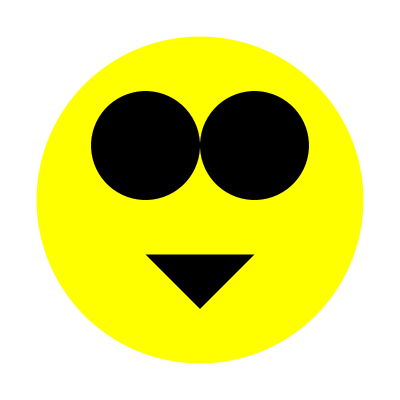

```mathematica
Graphics[{Yellow, Disk[{0, 0}, 3], Black, Disk[{-1, 1}, 1],Black, Disk[{1, 1}, 1], Black, Triangle[{{-1, -1}, {1, -1}, {0, -2}}]}]
```

```mathematica
RandomSample[Range[20], 20]
```

{12,1,17,14,8,20,18,16,13,11,7,9,2,5,3,15,6,4,19,10}

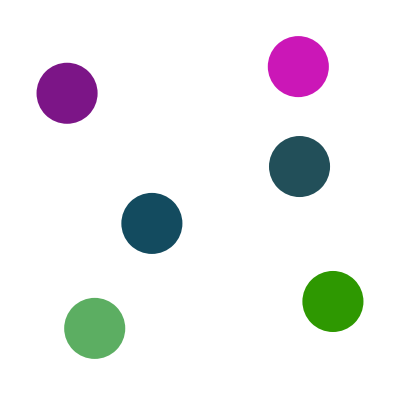

```mathematica
Graphics[Flatten[Table[{RandomColor[],Disk[{Random[], Random[]}, 0.1]}, {i, 6}]]]
```

## 5

```mathematica
randomColors=Table[RandomColor[], {i, 10}]
darkerRandomColors = Darker/@randomColors
Table[ColorNegate[c], {c, darkerRandomColors}]
```

{RGBColor[0.548986509263784, 0.9139482476539431, 0.044699123138624675],RGBColor[0.8781063182736175, 0.4262945760858792, 0.15754077076720763],RGBColor[0.6270386061251865, 0.8360143020800999, 0.8089011376870692],RGBColor[0.6791935707324999, 0.5649507779860299, 0.34824718209834526],RGBColor[0.4152035191985306, 0.6950312477122613, 0.9293562345774384],RGBColor[0.11885075562247716, 0.38726186946255203, 0.45864971568536994],RGBColor[0.17237423537002283, 0.11071828030374231, 0.07081746049835491],RGBColor[0.6390069762133761, 0.7099061055427585, 0.8708826410526951],RGBColor[0.00015252723348657682, 0.9911760640271283, 0.3018185808817446],RGBColor[0.25222086857103587, 0.9271070327809405, 0.561861903748641]}

{RGBColor[0.365991006175856, 0.6092988317692954, 0.029799415425749785],RGBColor[0.5854042121824117, 0.2841963840572528, 0.10502718051147175],RGBColor[0.418025737416791, 0.5573428680533999, 0.5392674251247128],RGBColor[0.4527957138216666, 0.3766338519906866, 0.2321647880655635],RGBColor[0.27680234613235377, 0.46335416514150757, 0.6195708230516257],RGBColor[0.07923383708165144, 0.2581745796417014, 0.30576647712357996],RGBColor[0.11491615691334855, 0.07381218686916155, 0.04721164033223661],RGBColor[0.4260046508089174, 0.47327073702850564, 0.5805884273684634],RGBColor[0.00010168482232438455, 0.6607840426847522, 0.20121238725449642],RGBColor[0.16814724571402392, 0.6180713551872937, 0.374574602499094]}

{RGBColor[0.634008993824144, 0.39070116823070455, 0.9702005845742502],RGBColor[0.4145957878175883, 0.7158036159427472, 0.8949728194885282],RGBColor[0.581974262583209, 0.44265713194660006, 0.4607325748752872],RGBColor[0.5472042861783334, 0.6233661480093133, 0.7678352119344365],RGBColor[0.7231976538676462, 0.5366458348584924, 0.3804291769483743],RGBColor[0.9207661629183486, 0.7418254203582986, 0.69423352287642],RGBColor[0.8850838430866514, 0.9261878131308384, 0.9527883596677634],RGBColor[0.5739953491910825, 0.5267292629714944, 0.4194115726315366],RGBColor[0.9998983151776756, 0.3392159573152478, 0.7987876127455036],RGBColor[0.831852754285976, 0.3819286448127063, 0.625425397500906]}

```mathematica
Graphics[{Yellow, Disk[{0, 0}, 3], Black, Disk[{-1, 1}, 1],Black, Disk[{1, 1}, 1], Black, Triangle[{{-1, -1}, {1, -1}, {0, -2}}]}]
```

-Graphics-

```mathematica
RandomSample[Range[20], 20]
```

{12,1,17,14,8,20,18,16,13,11,7,9,2,5,3,15,6,4,19,10}

```mathematica
Graphics[Flatten[Table[{RandomColor[],Disk[{Random[], Random[]}, 0.1]}, {i, 6}]]]
```

-Graphics-

## 5

```mathematica
randomColors=Table[RandomColor[], {i, 10}]
darkerRandomColors = Darker/@randomColors
Table[ColorNegate[c], {c, darkerRandomColors}]
```

{RGBColor[0.548986509263784, 0.9139482476539431, 0.044699123138624675],RGBColor[0.8781063182736175, 0.4262945760858792, 0.15754077076720763],RGBColor[0.6270386061251865, 0.8360143020800999, 0.8089011376870692],RGBColor[0.6791935707324999, 0.5649507779860299, 0.34824718209834526],RGBColor[0.4152035191985306, 0.6950312477122613, 0.9293562345774384],RGBColor[0.11885075562247716, 0.38726186946255203, 0.45864971568536994],RGBColor[0.17237423537002283, 0.11071828030374231, 0.07081746049835491],RGBColor[0.6390069762133761, 0.7099061055427585, 0.8708826410526951],RGBColor[0.00015252723348657682, 0.9911760640271283, 0.3018185808817446],RGBColor[0.25222086857103587, 0.9271070327809405, 0.561861903748641]}

{RGBColor[0.365991006175856, 0.6092988317692954, 0.029799415425749785],RGBColor[0.5854042121824117, 0.2841963840572528, 0.10502718051147175],RGBColor[0.418025737416791, 0.5573428680533999, 0.5392674251247128],RGBColor[0.4527957138216666, 0.3766338519906866, 0.2321647880655635],RGBColor[0.27680234613235377, 0.46335416514150757, 0.6195708230516257],RGBColor[0.07923383708165144, 0.2581745796417014, 0.30576647712357996],RGBColor[0.11491615691334855, 0.07381218686916155, 0.04721164033223661],RGBColor[0.4260046508089174, 0.47327073702850564, 0.5805884273684634],RGBColor[0.00010168482232438455, 0.6607840426847522, 0.20121238725449642],RGBColor[0.16814724571402392, 0.6180713551872937, 0.374574602499094]}

{RGBColor[0.634008993824144, 0.39070116823070455, 0.9702005845742502],RGBColor[0.4145957878175883, 0.7158036159427472, 0.8949728194885282],RGBColor[0.581974262583209, 0.44265713194660006, 0.4607325748752872],RGBColor[0.5472042861783334, 0.6233661480093133, 0.7678352119344365],RGBColor[0.7231976538676462, 0.5366458348584924, 0.3804291769483743],RGBColor[0.9207661629183486, 0.7418254203582986, 0.69423352287642],RGBColor[0.8850838430866514, 0.9261878131308384, 0.9527883596677634],RGBColor[0.5739953491910825, 0.5267292629714944, 0.4194115726315366],RGBColor[0.9998983151776756, 0.3392159573152478, 0.7987876127455036],RGBColor[0.831852754285976, 0.3819286448127063, 0.625425397500906]}

```mathematica
Graphics[{Yellow, Disk[{0, 0}, 3], Black, Disk[{-1, 1}, 1],Black, Disk[{1, 1}, 1], Black, Triangle[{{-1, -1}, {1, -1}, {0, -2}}]}]
```

-Graphics-

```mathematica
RandomSample[Range[20], 20]
```

{12,1,17,14,8,20,18,16,13,11,7,9,2,5,3,15,6,4,19,10}

```mathematica
Graphics[Flatten[Table[{RandomColor[],Disk[{Random[], Random[]}, 0.1]}, {i, 6}]]]
```

-Graphics-

## 5

```mathematica
randomColors=Table[RandomColor[], {i, 10}]
darkerRandomColors = Darker/@randomColors
Table[ColorNegate[c], {c, darkerRandomColors}]
```

{RGBColor[0.548986509263784, 0.9139482476539431, 0.044699123138624675],RGBColor[0.8781063182736175, 0.4262945760858792, 0.15754077076720763],RGBColor[0.6270386061251865, 0.8360143020800999, 0.8089011376870692],RGBColor[0.6791935707324999, 0.5649507779860299, 0.34824718209834526],RGBColor[0.4152035191985306, 0.6950312477122613, 0.9293562345774384],RGBColor[0.11885075562247716, 0.38726186946255203, 0.45864971568536994],RGBColor[0.17237423537002283, 0.11071828030374231, 0.07081746049835491],RGBColor[0.6390069762133761, 0.7099061055427585, 0.8708826410526951],RGBColor[0.00015252723348657682, 0.9911760640271283, 0.3018185808817446],RGBColor[0.25222086857103587, 0.9271070327809405, 0.561861903748641]}

{RGBColor[0.365991006175856, 0.6092988317692954, 0.029799415425749785],RGBColor[0.5854042121824117, 0.2841963840572528, 0.10502718051147175],RGBColor[0.418025737416791, 0.5573428680533999, 0.5392674251247128],RGBColor[0.4527957138216666, 0.3766338519906866, 0.2321647880655635],RGBColor[0.27680234613235377, 0.46335416514150757, 0.6195708230516257],RGBColor[0.07923383708165144, 0.2581745796417014, 0.30576647712357996],RGBColor[0.11491615691334855, 0.07381218686916155, 0.04721164033223661],RGBColor[0.4260046508089174, 0.47327073702850564, 0.5805884273684634],RGBColor[0.00010168482232438455, 0.6607840426847522, 0.20121238725449642],RGBColor[0.16814724571402392, 0.6180713551872937, 0.374574602499094]}

{RGBColor[0.634008993824144, 0.39070116823070455, 0.9702005845742502],RGBColor[0.4145957878175883, 0.7158036159427472, 0.8949728194885282],RGBColor[0.581974262583209, 0.44265713194660006, 0.4607325748752872],RGBColor[0.5472042861783334, 0.6233661480093133, 0.7678352119344365],RGBColor[0.7231976538676462, 0.5366458348584924, 0.3804291769483743],RGBColor[0.9207661629183486, 0.7418254203582986, 0.69423352287642],RGBColor[0.8850838430866514, 0.9261878131308384, 0.9527883596677634],RGBColor[0.5739953491910825, 0.5267292629714944, 0.4194115726315366],RGBColor[0.9998983151776756, 0.3392159573152478, 0.7987876127455036],RGBColor[0.831852754285976, 0.3819286448127063, 0.625425397500906]}

```mathematica
Graphics[{Yellow, Disk[{0, 0}, 3], Black, Disk[{-1, 1}, 1],Black, Disk[{1, 1}, 1], Black, Triangle[{{-1, -1}, {1, -1}, {0, -2}}]}]
```

-Graphics-

```mathematica
RandomSample[Range[20], 20]
```

{12,1,17,14,8,20,18,16,13,11,7,9,2,5,3,15,6,4,19,10}

```mathematica
Graphics[Flatten[Table[{RandomColor[],Disk[{Random[], Random[]}, 0.1]}, {i, 6}]]]
```

-Graphics-

## 5

```mathematica
randomColors=Table[RandomColor[], {i, 10}]
darkerRandomColors = Darker/@randomColors
Table[ColorNegate[c], {c, darkerRandomColors}]
```

{RGBColor[0.548986509263784, 0.9139482476539431, 0.044699123138624675],RGBColor[0.8781063182736175, 0.4262945760858792, 0.15754077076720763],RGBColor[0.6270386061251865, 0.8360143020800999, 0.8089011376870692],RGBColor[0.6791935707324999, 0.5649507779860299, 0.34824718209834526],RGBColor[0.4152035191985306, 0.6950312477122613, 0.9293562345774384],RGBColor[0.11885075562247716, 0.38726186946255203, 0.45864971568536994],RGBColor[0.17237423537002283, 0.11071828030374231, 0.07081746049835491],RGBColor[0.6390069762133761, 0.7099061055427585, 0.8708826410526951],RGBColor[0.00015252723348657682, 0.9911760640271283, 0.3018185808817446],RGBColor[0.25222086857103587, 0.9271070327809405, 0.561861903748641]}

{RGBColor[0.365991006175856, 0.6092988317692954, 0.029799415425749785],RGBColor[0.5854042121824117, 0.2841963840572528, 0.10502718051147175],RGBColor[0.418025737416791, 0.5573428680533999, 0.5392674251247128],RGBColor[0.4527957138216666, 0.3766338519906866, 0.2321647880655635],RGBColor[0.27680234613235377, 0.46335416514150757, 0.6195708230516257],RGBColor[0.07923383708165144, 0.2581745796417014, 0.30576647712357996],RGBColor[0.11491615691334855, 0.07381218686916155, 0.04721164033223661],RGBColor[0.4260046508089174, 0.47327073702850564, 0.5805884273684634],RGBColor[0.00010168482232438455, 0.6607840426847522, 0.20121238725449642],RGBColor[0.16814724571402392, 0.6180713551872937, 0.374574602499094]}

{RGBColor[0.634008993824144, 0.39070116823070455, 0.9702005845742502],RGBColor[0.4145957878175883, 0.7158036159427472, 0.8949728194885282],RGBColor[0.581974262583209, 0.44265713194660006, 0.4607325748752872],RGBColor[0.5472042861783334, 0.6233661480093133, 0.7678352119344365],RGBColor[0.7231976538676462, 0.5366458348584924, 0.3804291769483743],RGBColor[0.9207661629183486, 0.7418254203582986, 0.69423352287642],RGBColor[0.8850838430866514, 0.9261878131308384, 0.9527883596677634],RGBColor[0.5739953491910825, 0.5267292629714944, 0.4194115726315366],RGBColor[0.9998983151776756, 0.3392159573152478, 0.7987876127455036],RGBColor[0.831852754285976, 0.3819286448127063, 0.625425397500906]}

```mathematica
Graphics[{Yellow, Disk[{0, 0}, 3], Black, Disk[{-1, 1}, 1],Black, Disk[{1, 1}, 1], Black, Triangle[{{-1, -1}, {1, -1}, {0, -2}}]}]
```

-Graphics-

```mathematica
RandomSample[Range[20], 20]
```

{12,1,17,14,8,20,18,16,13,11,7,9,2,5,3,15,6,4,19,10}

```mathematica
Graphics[Flatten[Table[{RandomColor[],Disk[{Random[], Random[]}, 0.1]}, {i, 6}]]]
```

-Graphics-

## 2

1. Foo[a, b, c]
2. blue
3.

```mathematica
3*6
```

18

```mathematica
1+1
```

2

```mathematica
4*6/2
```

12

```mathematica
3+12
```

15

```mathematica
8-5
```

3

4.

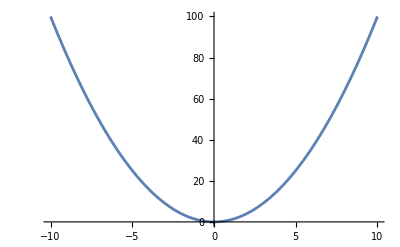

```mathematica
Plot[x^2, {x, -10, 10}]
```

6.

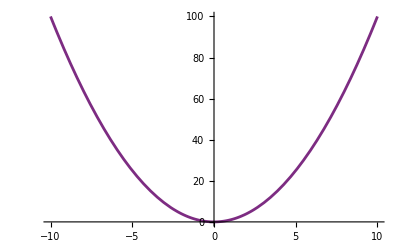

```mathematica
Plot[x^2, {x, -10, 10}, ColorFunction->"Rainbow"]
```

## 3

```mathematica
number=8;
number ^ 2
```

64

```mathematica
image=-Graphics-
Blur[image]
```

-Graphics-

-Graphics-

```mathematica
randBlurredImage:=Blur[image,10*Random[]]
randBlurredImage
```

-Graphics-

```mathematica
BlurFunc[im_]:=Blur[im]
```

```mathematica
Mul[x_,y_]:=x*y
```

## 2

1. Foo[a, b, c]
2. blue
3.

```mathematica
3*6
```

18

```mathematica
1+1
```

2

```mathematica
4*6/2
```

12

```mathematica
3+12
```

15

```mathematica
8-5
```

3

4.

```mathematica
Plot[x^2, {x, -10, 10}]
```

-Graphics-

6.

```mathematica
Plot[x^2, {x, -10, 10}, ColorFunction->"Rainbow"]
```

-Graphics-

## 1

Try to find a clear plastic bag that has a squishy, dry, sliced, brown solid called bread. Open the bag by untwisting the one end with a clip on it, and take out two pieces of bread. Place each slice face down on a counter next to one another.

Take out a cylinder with the word ‘peanut butter' on the front. Twist the top counterclockwise while holding the bottom. Repeat for jelly. Find a flat, elongated, pointed object called a knife and pick it up by the less flattened side called the handle. Direct the non-handle end into the peanut butter, raise it back out, and place the knife on one end of the bread. Move the knife to the other side of the bread while keeping in contact with it. Repeat for jelly. Put both slices together with the faces, which are the sides which the condiment was placed on, placed inward.

# New Layout

## Computational Art Project

```mathematica
baseImage = ExampleData[{"TestImage", "House"}]
```

-Graphics-

```mathematica
scale=20;
shapeType=RandomInteger[{3, 6}];
RandomShapeAtPos[pos_]:=Polygon[Table[pos+{scale*Random[],scale*Random[]}, {i, shapeType}]];
Graphics[Join[{baseImage}, Flatten[{{RandomChoice[DominantColors[baseImage]],RandomShapeAtPos[#]}&/@Table[{10*scale*Random[], 10*scale*Random[]}, {i, 100}]}]]]
```

-Graphics-

## 7

```mathematica
s=StringJoin[{"Wolfram", "Language"}]
StringLength[s]
```

WolframLanguage

15

```mathematica
Length[%]
```

0

```mathematica
Part[Alphabet["Arabic"], Length[Alphabet["Arabic"]]/2]
```

ص

```mathematica
s="testing sentence"
StringSplit[s]
TextSentences[s]
```

testing sentence

{testing,sentence}

{testing sentence}

## 8

“_” = Blank[] = one thing that can be anything
MatchQ[{1, 2, 3}, {_, 2, _}] = True
“__” = BlankSequence[] = one or more things
MatchQ[{1, 2, 3}, {__, 3}] = True
“___” = BlankNullSequence[] = zero or more things

```mathematica
StringMatchQ["Fun","F"~~__~~"n"]
```

True

```mathematica
Select[{{a,b},{b,e,h,f},{b},{e,d,b},{b,c},{5,b}}, MatchQ[#,{_, b}]&]
```

{{a,b},{5,b}}

```mathematica
StringJoin[Reverse[AlphabeticSort[Select[Characters["i am learning wolfram language"], #!=" "&]]]]
```

wurronnnmmllliigggfeeaaaaa

## Computational Haiku

```mathematica
Syllables=Length[ResourceFunction["WordSyllables"][#]]&;

baseString="Over the __(adjective)__
Forest, winds howl in __(noun)__
With no leaves to __(verb)__."

wordsByLine =StringSplit[#, {" ", "."}]&/@StringSplit[baseString, "\n"];

syllabesPerLine=Plus@@@((Syllables/@#)&/@(Drop[#, -1]&/@wordsByLine));
neededWordSyllables={5, 7, 5}-syllabesPerLine;
neededWordTypes=#[[-1]]&/@wordsByLine;

RandomNSyllableWord=Function[{type, syllables}, Module[{W=RandomWord[type]}, While[!Syllables[W]==syllables,W=RandomWord[type]]; W]];

StringJoin[Riffle[Riffle[#, " "]&/@Table[Append[Drop[wordsByLine[[i]], -1], Replace[neededWordTypes[[i]],
{"__(adjective)__"->RandomNSyllableWord["Adjective",neededWordSyllables[[i]]],
"__(noun)__"->RandomNSyllableWord["Noun",neededWordSyllables[[i]]],
"__(verb)__"->RandomNSyllableWord["Verb",neededWordSyllables[[i]]]}
]], {i, 3}], "\n"]]<>"."
```

Over the __(adjective)__
Forest, winds howl in __(noun)__
With no leaves to __(verb)__.

Over the chary
Forest, winds howl in bebop
With no leaves to buzz.

## 10

SoundNote[A0,1,Marimba]

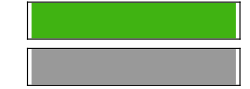

```mathematica
A=SoundNote["A0", 1, "Marimba"]
Sound[A]
```

```mathematica
Play[Sin[440*t], {t, 0, 10}]
```

-Graphics-

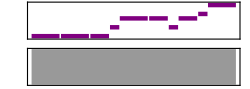

-Graphics-

```mathematica
notes={"C","C","C","D","E","E","D","E","F","G"};
noteLengths={1.5,1.5,1,0.5,1.5,1,0.5,1,0.5,1.5}/2;
Sound[SoundNote@@#&/@Transpose[{notes, noteLengths}]]
LowpassFilter[Sound[SoundNote@@#&/@Transpose[{notes, noteLengths}]], 2000]
```

```mathematica
Spectrogram[Sound[SoundNote@@#&/@Transpose[{notes, noteLengths}]]]
Spectrogram[LowpassFilter[Sound[SoundNote@@#&/@Transpose[{notes, noteLengths}]], 400]]
```

-Graphics-

-Graphics-

## 11

```mathematica
With[{x=10}, x^2]
Block[{x=10, y},y=x+1; y^2]
Module[{x=10}, x^2]
```

100

121

100

use Module, as Block does weird stuff internally but is basically the same

## 12

```mathematica
D1=Dataset[ResourceData["Mister Rogers' Sweater Colors"]];
D1[[1]]
C1={#["EpisodeNumber"], #["SweaterColor"]}&/@D1;
C1[[1]]
TimeSeries[C1]
```

TimeSeries::ntprs: The argument Dataset[«302»] at position 1 is expected to be a list of time-value pairs or a list of states with equal dimensionality.

TimeSeries[]

## Audio Visualization Project

```mathematica
baseAudio=ResourceData["Sample Audio: Apollo 11 One Small Step"]
```

```mathematica
D1=AudioData[baseAudio][[1]];
G1=Graphics[{Point[{-1, -1}], Point[{1, 1}],Rectangle[{0, 0}, {1, #}]}]&/@D1;
V=SlideShowVideo[G1, DefaultDuration->Duration[baseAudio]];
```

```mathematica
VideoCombine[{V, baseAudio}]
```